### Categorization

Tutorial

DoFun

DoFun`

DoFun/tutorial/Scalar O(N) symmetric theory

### Keywords

Details

# Scalar O(N) symmetric theory

This tutorial describes the derivations of the FRGEs of a scalar O(N) symmetric theory.

XXXX | XXXX
XXXX | XXXX
XXXX | XXXX

```mathematica
Needs["DoFun`"]
```

## Symmetric phase

### Symbolic derivation

The first thing we need is the action in symbolic form. The following definition gives an action with a field phi which only possess interactions with an even number of fields involved up to the ten-point functions. Including terms up to this order guarantees we get all terms.

```mathematica
actionONSymbolic={{phi,10,even}};
```

The flow equations is obtained with the command doRGE:

```mathematica
zeroPoint = doRGE[actionONSymbolic, {}]
```

1/2 op[dR[{phi,r1},{phi,s1}],P[{phi,s1},{phi,r1}]]

The empty list {} tells doRGE that we want the flow equation of the effective average action.

Such symbolic output can be represented graphically with RGEPlot. It is useful to choose a graphical style for the field.

```mathematica
fieldStyleON = {{phi, Black}};
```

For RGEPlot we use the option output->forceEquation to show the result in form of an equation.

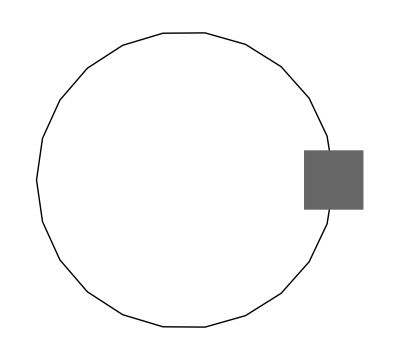
Γ^k∂_t ^= | -Graphics-+1/2^ |  |  |

```mathematica
RGEPlot[zeroPoint,fieldStyleON,output->forceEquation]
```

For the flow of the two-point function we replace the empty list by a list of two-fields:

```mathematica
twoPoint=doRGE[actionONSymbolic,{phi,phi}]
```

1/2 op[dR[{phi,r1},{phi,s1}],P[{phi,t1},{phi,r1}],P[{phi,s1},{phi,v1}],V[{phi,i1},{phi,i2},{phi,v1},{phi,t1}]]

The graphical representation is

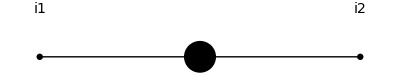
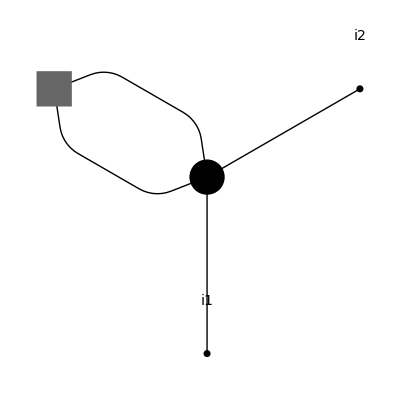
-Graphics-∂_t ^-1= | -Graphics-+1/2^ |  |  |

```mathematica
RGEPlot[twoPoint, fieldStyleON, output -> forceEquation]
```

For higher n-point functions the procedure is completely the same. E.g., for the four-point function we get

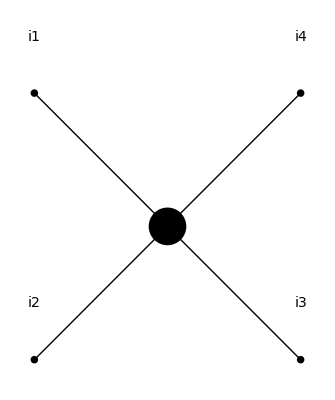
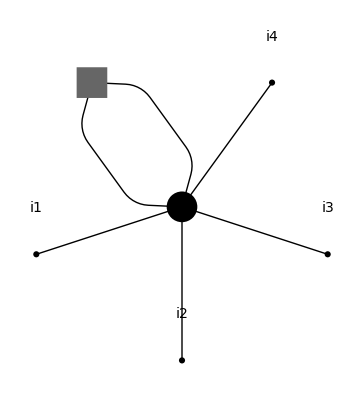
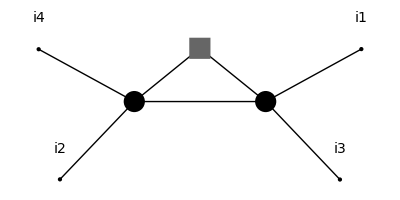
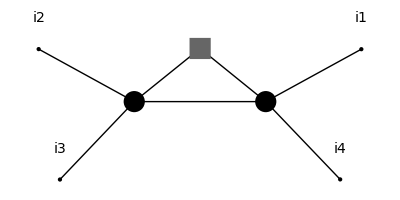
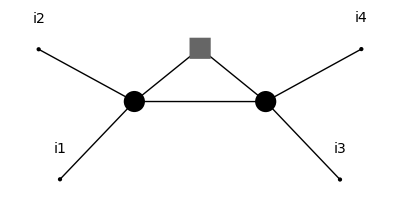
-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--^ | -Graphics--^ | -Graphics--^

```mathematica
fourPoint=doRGE[actionONSymbolic,{phi,phi,phi,phi}];
RGEPlot[fourPoint,fieldStyleON]
```

We can use another ansatz for the effective average action that realizes a truncation at four-point level. Then the first diagramm vanishes.

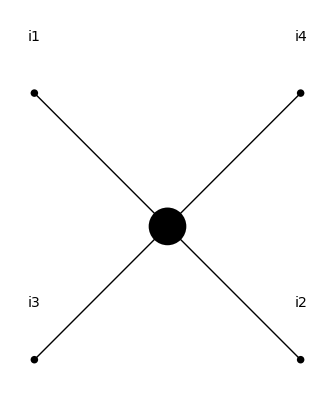
-Graphics-∂_t ^= | -Graphics--^ | -Graphics--^ | -Graphics--^ |

```mathematica
actionONSTrunc2={{phi,4,even}};
fourPointTrunc=doRGE[actionONSTrunc2,{phi,phi,phi,phi}];
RGEPlot[fourPointTrunc,fieldStyleON]
```

If we want to use our results later on again, we can export them with Put and importn them with Get. For instance:

```mathematica
Put[fourPoint,"4Point.rge"]
```

```mathematica
fourPointImport = Get["4Point.rge"];
RGEPlot[fourPointImport, fieldStyleON, output -> forceEquation]
```

-Graphics-∂_t ^= | -Graphics--1/2^ | -Graphics--^ | -Graphics--^ | -Graphics--^

### Algebraic expressions

Next we derive the algebraic expressions from the symbolic one obtained with doRGE.

For this we require the Feynman rules of propagators and vertices. The command getFR assists in this task.

Before we define the details of the ansatz for the effective average action we declare what indices the field phi has with defineFieldsSpecific. The first entry is always the momentum, the second one here is the O(N) index:

```mathematica
defineFieldsSpecific[{phi[momentum,type]}];
```

Then we can define the ansatz for the effective average action in momentum space. We take a four-point truncation.

```mathematica
actionON2=convertAction[1/2 (p^2 Z[p^2]+R[k])op[phi[p,i],phi[-p,i]]+lambda2/8op[phi[p,i],phi[q,i],phi[r,j],phi[-p-q-r,j]]]
```

1/8 lambda2 op[phi[q$8533,dummy[218]],phi[q$8534,dummy[218]],phi[q$8535,dummy[219]],phi[-q$8533-q$8534-q$8535,dummy[219]]]+1/2 op[phi[q$8537,dummy[220]],phi[-q$8537,dummy[220]]] R[k]+1/2 q$8539^2 op[phi[q$8539,dummy[221]],phi[-q$8539,dummy[221]]] Z[q$8539^2]

The command convertAction is required to rewrite our input into DoFun notation, where q$i represents a momentum integral.

This derives the two- and four-point functions:

```mathematica
FM2=getFR[actionON2,{phi[p1,i],phi[p2,j]}]
```

delta[type,i,j] deltam[p1+p2] R[k]+p1^2 delta[type,i,j] deltam[p1+p2] Z[p1^2]

```mathematica
FM4=getFR[actionON2,{phi[p1,i],phi[p2,j],phi[p3,l],phi[p4,m]}]
```

-lambda2 delta[type,i,m] delta[type,j,l] deltam[p1+p2+p3+p4]-lambda2 delta[type,i,l] delta[type,j,m] deltam[p1+p2+p3+p4]-lambda2 delta[type,i,j] delta[type,l,m] deltam[p1+p2+p3+p4]

The propagator we obtain by inverting the two-point function. This tells DoFun what the propagator of a phi field looks like:

```mathematica
P[phi[p1_, a_], phi[p2_, b_], explicit -> True] := (delta[type, a, b])/(Z[p1^2] + R[p1^2, k]);
```

Note the option explicit->True.

The regulator insertion needs also to be defined:

```mathematica
dR[phi[p1_,a_],phi[p2_,b_],explicit->True]:=delta[type,a,b]dR[p1^2,k];
```

For the four-point function we use the result we obtained with getFR, where we discard the delta distribution:

```mathematica
V[phi[p1_,i_],phi[p2_,j_],phi[p3_,l_],phi[p4_,m_],explicit->True]=FM4/deltam[p1+p2+p3+p4]//Expand;
```

Now we can derive the integrands of the right-hand side of the flow equations for the effective average action, the two- and the four-point functions with getAE:

```mathematica
zeroPointAlg=Plus@@getAE[zeroPoint,{}]//integrateDeltas
```

(dim[type] dR[q1^2,k])/(2 (R[q1^2,k]+Z[q1^2]))

dim[type] is the dimension of the index type, i.e., for O(N) it is N. integrateDeltas was employed to contract Kronecker deltas.

The conversion of the two-point function expression requires additional input in the second argument. The entry {phi, i1, p1, i} tells getAE that there the leg of the field phi with symbolic index i1 corresponds to a leg with the momentum p1 and the O(N) index i.

```mathematica
twoPointAlg=Plus@@getAE[twoPoint,{{phi,i1,p1,i},{phi,i2,p2,j}}]//integrateDeltas
```

-(lambda2 delta[type,i,j] dR[(p1+p2+q1)^2,k])/((R[(-p1-p2-q1)^2,k]+Z[(-p1-p2-q1)^2]) (R[q1^2,k]+Z[q1^2]))-(lambda2 delta[type,i,j] dim[type] dR[(p1+p2+q1)^2,k])/(2 (R[(-p1-p2-q1)^2,k]+Z[(-p1-p2-q1)^2]) (R[q1^2,k]+Z[q1^2]))

In the zero-momentum limit this becomes

```mathematica
twoPointAlg/.{p1:>0,p2:>0}//Simplify
```

-(lambda2 delta[type,i,j] (2+dim[type]) dR[q1^2,k])/(2 (R[q1^2,k]+Z[q1^2])^2)

For the four-point function we directly derive the zero-momentum result:

```mathematica
fourPointAlg=Plus@@getAE[fourPointTrunc,{{phi,i1,0,i},{phi,i2,0,j},{phi,i3,0,l},{phi,i4,0,m}}]//integrateDeltas//Simplify
```

-(lambda2^2 (delta[type,i,m] delta[type,j,l]+delta[type,i,l] delta[type,j,m]+delta[type,i,j] delta[type,l,m]) (8+dim[type]) dR[q1^2,k])/(R[q1^2,k]+Z[q1^2])^3

This can be projected with the tensor from the left-hand side of the equation:

```mathematica
lhs=V[phi[0,i],phi[0,j],phi[0,l],phi[0,m],explicit->True]V[phi[0,i],phi[0,j],phi[0,l],phi[0,m],explicit->True]/λ2^2//integrateDeltas;
V[phi[0,i],phi[0,j],phi[0,l],phi[0,m],explicit->True]/λ2/lhs fourPointAlg//integrateDeltas//Simplify
```

(lambda2 λ2 (8+dim[type]) dR[q1^2,k])/((R[q1^2,k]+Z[q1^2])^3)

## Symmetry broken phase

More About

Related Tutorials

Related Wolfram Education Group Courses